## problem

4th and 8th are missing intersection

apparently 6th has 6 intersections instead of only 5?

```mathematica
intersection[{{x1_,y1_},{x2_,y2_}},{{x3_,y3_},{x4_,y4_}}]:=
Module[{d,u12,u34,y43,x21,x43,y21,y13,x13,x,y},
y43=(y4-y3);
x21=(x2-x1);
x43=(x4-x3);
y21=(y2-y1);
y13=(y1-y3);
x13=(x1-x3);
d=y43 x21-x43 y21;
If[d==0,Return[$Failed1]];
{u12,u34}={(x43 y13-y43 x13)/d,(x21 y13-y21 x13)/d};
If[(0≤u12≤1)&&(0≤u34≤1),
x=x1+u12 (x2-x1);
y=y1+u12 (y2-y1);
{x,y}
,
$Failed2]
]
```

## points

up:
1
08-19 18:00:35.186: DEBUG/touch(17531): DOWN <30.0,290.0>
08-19 18:00:35.209: DEBUG/touch(17531): MOVE <30.0,290.0>
08-19 18:00:35.224: DEBUG/touch(17531): MOVE <30.0,290.0>
08-19 18:00:35.248: DEBUG/touch(17531): MOVE <30.0,280.0>
08-19 18:00:35.271: DEBUG/touch(17531): MOVE <40.0,270.0>
08-19 18:00:35.287: DEBUG/touch(17531): MOVE <50.0,260.0>
08-19 18:00:35.303: DEBUG/touch(17531): MOVE <80.0,220.0>
08-19 18:00:35.320: DEBUG/touch(17531): MOVE <110.0,180.0>
08-19 18:00:35.334: DEBUG/touch(17531): MOVE <130.0,150.0>
08-19 18:00:35.357: DEBUG/touch(17531): MOVE <160.0,110.0>
08-19 18:00:35.373: DEBUG/touch(17531): MOVE <190.0,80.0>
08-19 18:00:35.389: DEBUG/touch(17531): MOVE <200.0,60.0>
08-19 18:00:35.412: DEBUG/touch(17531): MOVE <220.0,40.0>
08-19 18:00:35.428: DEBUG/touch(17531): MOVE <230.0,20.0>
08-19 18:00:35.443: DEBUG/touch(17531): MOVE <230.0,20.0>
08-19 18:00:35.467: DEBUG/touch(17531): MOVE <240.0,10.0>
08-19 18:00:35.475: DEBUG/touch(17531): UP   <240.0,10.0>

```mathematica
dat1="08-19 18:00:35.186: DEBUG/touch(17531): DOWN <30.0,290.0>
08-19 18:00:35.209: DEBUG/touch(17531): MOVE <30.0,290.0>
08-19 18:00:35.224: DEBUG/touch(17531): MOVE <30.0,290.0>
08-19 18:00:35.248: DEBUG/touch(17531): MOVE <30.0,280.0>
08-19 18:00:35.271: DEBUG/touch(17531): MOVE <40.0,270.0>
08-19 18:00:35.287: DEBUG/touch(17531): MOVE <50.0,260.0>
08-19 18:00:35.303: DEBUG/touch(17531): MOVE <80.0,220.0>
08-19 18:00:35.320: DEBUG/touch(17531): MOVE <110.0,180.0>
08-19 18:00:35.334: DEBUG/touch(17531): MOVE <130.0,150.0>
08-19 18:00:35.357: DEBUG/touch(17531): MOVE <160.0,110.0>
08-19 18:00:35.373: DEBUG/touch(17531): MOVE <190.0,80.0>
08-19 18:00:35.389: DEBUG/touch(17531): MOVE <200.0,60.0>
08-19 18:00:35.412: DEBUG/touch(17531): MOVE <220.0,40.0>
08-19 18:00:35.428: DEBUG/touch(17531): MOVE <230.0,20.0>
08-19 18:00:35.443: DEBUG/touch(17531): MOVE <230.0,20.0>
08-19 18:00:35.467: DEBUG/touch(17531): MOVE <240.0,10.0>
08-19 18:00:35.475: DEBUG/touch(17531): UP   <240.0,10.0>";
line1=Flatten[StringCases[StringSplit[dat1,"\n"],__~~("DOWN"|"MOVE"|"UP  ")~~" <"~~Shortest[dat__]~~">"~~___:>ToExpression["{"~~dat~~"}"]],1];
ints1=Flatten[StringCases[StringSplit[dat1,"\n"],__~~("INTR")~~" <"~~Shortest[dat__]~~">"~~___:>ToExpression["{"~~dat~~"}"]],1];
```

2
08-19 18:00:36.201: DEBUG/touch(17531): DOWN <50.0,410.0>
08-19 18:00:36.240: DEBUG/touch(17531): MOVE <50.0,410.0>
08-19 18:00:36.295: DEBUG/touch(17531): MOVE <50.0,410.0>
08-19 18:00:36.311: DEBUG/touch(17531): MOVE <60.0,400.0>
08-19 18:00:36.334: DEBUG/touch(17531): MOVE <60.0,400.0>
08-19 18:00:36.351: DEBUG/touch(17531): MOVE <90.0,360.0>
08-19 18:00:36.373: DEBUG/touch(17531): MOVE <120.0,330.0>
08-19 18:00:36.389: DEBUG/touch(17531): MOVE <150.0,290.0>
08-19 18:00:36.404: DEBUG/touch(17531): MOVE <170.0,260.0>
08-19 18:00:36.428: DEBUG/touch(17531): MOVE <220.0,200.0>
08-19 18:00:36.451: DEBUG/touch(17531): MOVE <240.0,170.0>
08-19 18:00:36.474: DEBUG/touch(17531): MOVE <300.0,100.0>
08-19 18:00:36.498: DEBUG/touch(17531): MOVE <310.0,90.0>
08-19 18:00:36.560: DEBUG/touch(17531): MOVE <340.0,50.0>
08-19 18:00:36.568: DEBUG/touch(17531): UP   <340.0,50.0>

```mathematica
dat2="08-19 18:00:36.201: DEBUG/touch(17531): DOWN <50.0,410.0>
08-19 18:00:36.240: DEBUG/touch(17531): MOVE <50.0,410.0>
08-19 18:00:36.295: DEBUG/touch(17531): MOVE <50.0,410.0>
08-19 18:00:36.311: DEBUG/touch(17531): MOVE <60.0,400.0>
08-19 18:00:36.334: DEBUG/touch(17531): MOVE <60.0,400.0>
08-19 18:00:36.351: DEBUG/touch(17531): MOVE <90.0,360.0>
08-19 18:00:36.373: DEBUG/touch(17531): MOVE <120.0,330.0>
08-19 18:00:36.389: DEBUG/touch(17531): MOVE <150.0,290.0>
08-19 18:00:36.404: DEBUG/touch(17531): MOVE <170.0,260.0>
08-19 18:00:36.428: DEBUG/touch(17531): MOVE <220.0,200.0>
08-19 18:00:36.451: DEBUG/touch(17531): MOVE <240.0,170.0>
08-19 18:00:36.474: DEBUG/touch(17531): MOVE <300.0,100.0>
08-19 18:00:36.498: DEBUG/touch(17531): MOVE <310.0,90.0>
08-19 18:00:36.560: DEBUG/touch(17531): MOVE <340.0,50.0>
08-19 18:00:36.568: DEBUG/touch(17531): UP   <340.0,50.0>";
line2=Flatten[StringCases[StringSplit[dat2,"\n"],__~~("DOWN"|"MOVE"|"UP  ")~~" <"~~Shortest[dat__]~~">"~~___:>ToExpression["{"~~dat~~"}"]],1];
ints2=Flatten[StringCases[StringSplit[dat2,"\n"],__~~("INTR")~~" <"~~Shortest[dat__]~~">"~~___:>ToExpression["{"~~dat~~"}"]],1];
```

3
08-19 18:00:37.287: DEBUG/touch(17531): DOWN <60.0,540.0>
08-19 18:00:37.318: DEBUG/touch(17531): MOVE <60.0,540.0>
08-19 18:00:37.334: DEBUG/touch(17531): MOVE <60.0,540.0>
08-19 18:00:37.350: DEBUG/touch(17531): MOVE <60.0,540.0>
08-19 18:00:37.373: DEBUG/touch(17531): MOVE <70.0,530.0>
08-19 18:00:37.389: DEBUG/touch(17531): MOVE <80.0,510.0>
08-19 18:00:37.404: DEBUG/touch(17531): MOVE <140.0,460.0>
08-19 18:00:37.428: DEBUG/touch(17531): MOVE <160.0,430.0>
08-19 18:00:37.451: DEBUG/touch(17531): MOVE <170.0,420.0>
08-19 18:00:37.467: DEBUG/touch(17531): MOVE <190.0,380.0>
08-19 18:00:37.482: DEBUG/touch(17531): MOVE <200.0,360.0>
08-19 18:00:37.498: DEBUG/touch(17531): MOVE <250.0,290.0>
08-19 18:00:37.514: DEBUG/touch(17531): MOVE <270.0,260.0>
08-19 18:00:37.537: DEBUG/touch(17531): MOVE <300.0,230.0>
08-19 18:00:37.553: DEBUG/touch(17531): MOVE <330.0,200.0>
08-19 18:00:37.568: DEBUG/touch(17531): MOVE <350.0,170.0>
08-19 18:00:37.592: DEBUG/touch(17531): MOVE <360.0,150.0>
08-19 18:00:37.607: DEBUG/touch(17531): MOVE <380.0,120.0>
08-19 18:00:37.623: DEBUG/touch(17531): MOVE <390.0,110.0>
08-19 18:00:37.639: DEBUG/touch(17531): MOVE <400.0,100.0>
08-19 18:00:37.662: DEBUG/touch(17531): MOVE <400.0,100.0>
08-19 18:00:37.662: DEBUG/touch(17531): UP   <400.0,100.0>

```mathematica
dat3="08-19 18:00:37.287: DEBUG/touch(17531): DOWN <60.0,540.0>
08-19 18:00:37.318: DEBUG/touch(17531): MOVE <60.0,540.0>
08-19 18:00:37.334: DEBUG/touch(17531): MOVE <60.0,540.0>
08-19 18:00:37.350: DEBUG/touch(17531): MOVE <60.0,540.0>
08-19 18:00:37.373: DEBUG/touch(17531): MOVE <70.0,530.0>
08-19 18:00:37.389: DEBUG/touch(17531): MOVE <80.0,510.0>
08-19 18:00:37.404: DEBUG/touch(17531): MOVE <140.0,460.0>
08-19 18:00:37.428: DEBUG/touch(17531): MOVE <160.0,430.0>
08-19 18:00:37.451: DEBUG/touch(17531): MOVE <170.0,420.0>
08-19 18:00:37.467: DEBUG/touch(17531): MOVE <190.0,380.0>
08-19 18:00:37.482: DEBUG/touch(17531): MOVE <200.0,360.0>
08-19 18:00:37.498: DEBUG/touch(17531): MOVE <250.0,290.0>
08-19 18:00:37.514: DEBUG/touch(17531): MOVE <270.0,260.0>
08-19 18:00:37.537: DEBUG/touch(17531): MOVE <300.0,230.0>
08-19 18:00:37.553: DEBUG/touch(17531): MOVE <330.0,200.0>
08-19 18:00:37.568: DEBUG/touch(17531): MOVE <350.0,170.0>
08-19 18:00:37.592: DEBUG/touch(17531): MOVE <360.0,150.0>
08-19 18:00:37.607: DEBUG/touch(17531): MOVE <380.0,120.0>
08-19 18:00:37.623: DEBUG/touch(17531): MOVE <390.0,110.0>
08-19 18:00:37.639: DEBUG/touch(17531): MOVE <400.0,100.0>
08-19 18:00:37.662: DEBUG/touch(17531): MOVE <400.0,100.0>
08-19 18:00:37.662: DEBUG/touch(17531): UP   <400.0,100.0>";
line3=Flatten[StringCases[StringSplit[dat3,"\n"],__~~("DOWN"|"MOVE"|"UP  ")~~" <"~~Shortest[dat__]~~">"~~___:>ToExpression["{"~~dat~~"}"]],1];
ints3=Flatten[StringCases[StringSplit[dat3,"\n"],__~~("INTR")~~" <"~~Shortest[dat__]~~">"~~___:>ToExpression["{"~~dat~~"}"]],1];
```

4th
08-19 18:00:38.256: DEBUG/touch(17531): DOWN <60.0,670.0>
08-19 18:00:38.303: DEBUG/touch(17531): MOVE <60.0,670.0>
08-19 18:00:38.310: DEBUG/touch(17531): MOVE <60.0,670.0>
08-19 18:00:38.326: DEBUG/touch(17531): MOVE <70.0,660.0>
08-19 18:00:38.342: DEBUG/touch(17531): MOVE <80.0,650.0>
08-19 18:00:38.365: DEBUG/touch(17531): MOVE <150.0,580.0>
08-19 18:00:38.381: DEBUG/touch(17531): MOVE <190.0,540.0>
08-19 18:00:38.396: DEBUG/touch(17531): MOVE <240.0,490.0>
08-19 18:00:38.420: DEBUG/touch(17531): MOVE <250.0,480.0>
08-19 18:00:38.435: DEBUG/touch(17531): MOVE <320.0,410.0>
08-19 18:00:38.459: DEBUG/touch(17531): MOVE <360.0,360.0>
08-19 18:00:38.474: DEBUG/touch(17531): MOVE <410.0,310.0>
08-19 18:00:38.498: DEBUG/touch(17531): MOVE <450.0,270.0>
08-19 18:00:38.514: DEBUG/touch(17531): MOVE <460.0,250.0>
08-19 18:00:38.537: DEBUG/touch(17531): MOVE <470.0,230.0>
08-19 18:00:38.537: DEBUG/touch(17531): UP   <470.0,230.0>

```mathematica
dat4="08-19 18:00:38.256: DEBUG/touch(17531): DOWN <60.0,670.0>
08-19 18:00:38.303: DEBUG/touch(17531): MOVE <60.0,670.0>
08-19 18:00:38.310: DEBUG/touch(17531): MOVE <60.0,670.0>
08-19 18:00:38.326: DEBUG/touch(17531): MOVE <70.0,660.0>
08-19 18:00:38.342: DEBUG/touch(17531): MOVE <80.0,650.0>
08-19 18:00:38.365: DEBUG/touch(17531): MOVE <150.0,580.0>
08-19 18:00:38.381: DEBUG/touch(17531): MOVE <190.0,540.0>
08-19 18:00:38.396: DEBUG/touch(17531): MOVE <240.0,490.0>
08-19 18:00:38.420: DEBUG/touch(17531): MOVE <250.0,480.0>
08-19 18:00:38.435: DEBUG/touch(17531): MOVE <320.0,410.0>
08-19 18:00:38.459: DEBUG/touch(17531): MOVE <360.0,360.0>
08-19 18:00:38.474: DEBUG/touch(17531): MOVE <410.0,310.0>
08-19 18:00:38.498: DEBUG/touch(17531): MOVE <450.0,270.0>
08-19 18:00:38.514: DEBUG/touch(17531): MOVE <460.0,250.0>
08-19 18:00:38.537: DEBUG/touch(17531): MOVE <470.0,230.0>
08-19 18:00:38.537: DEBUG/touch(17531): UP   <470.0,230.0>";
line4=Flatten[StringCases[StringSplit[dat4,"\n"],__~~("DOWN"|"MOVE"|"UP  ")~~" <"~~Shortest[dat__]~~">"~~___:>ToExpression["{"~~dat~~"}"]],1];
ints4=Flatten[StringCases[StringSplit[dat4,"\n"],__~~("INTR")~~" <"~~Shortest[dat__]~~">"~~___:>ToExpression["{"~~dat~~"}"]],1];
```

5
08-19 18:00:39.099: DEBUG/touch(17531): DOWN <130.0,760.0>
08-19 18:00:39.139: DEBUG/touch(17531): MOVE <130.0,760.0>
08-19 18:00:39.178: DEBUG/touch(17531): MOVE <140.0,760.0>
08-19 18:00:39.193: DEBUG/touch(17531): MOVE <140.0,750.0>
08-19 18:00:39.217: DEBUG/touch(17531): MOVE <180.0,720.0>
08-19 18:00:39.232: DEBUG/touch(17531): MOVE <230.0,670.0>
08-19 18:00:39.256: DEBUG/touch(17531): MOVE <280.0,610.0>
08-19 18:00:39.279: DEBUG/touch(17531): MOVE <330.0,560.0>
08-19 18:00:39.303: DEBUG/touch(17531): MOVE <370.0,510.0>
08-19 18:00:39.326: DEBUG/touch(17531): MOVE <390.0,480.0>
08-19 18:00:39.342: DEBUG/touch(17531): MOVE <430.0,430.0>
08-19 18:00:39.365: DEBUG/touch(17531): MOVE <460.0,400.0>
08-19 18:00:39.389: DEBUG/touch(17531): MOVE <470.0,390.0>
08-19 18:00:39.389: DEBUG/touch(17531): UP   <470.0,390.0>

```mathematica
dat5="08-19 18:00:39.099: DEBUG/touch(17531): DOWN <130.0,760.0>
08-19 18:00:39.139: DEBUG/touch(17531): MOVE <130.0,760.0>
08-19 18:00:39.178: DEBUG/touch(17531): MOVE <140.0,760.0>
08-19 18:00:39.193: DEBUG/touch(17531): MOVE <140.0,750.0>
08-19 18:00:39.217: DEBUG/touch(17531): MOVE <180.0,720.0>
08-19 18:00:39.232: DEBUG/touch(17531): MOVE <230.0,670.0>
08-19 18:00:39.256: DEBUG/touch(17531): MOVE <280.0,610.0>
08-19 18:00:39.279: DEBUG/touch(17531): MOVE <330.0,560.0>
08-19 18:00:39.303: DEBUG/touch(17531): MOVE <370.0,510.0>
08-19 18:00:39.326: DEBUG/touch(17531): MOVE <390.0,480.0>
08-19 18:00:39.342: DEBUG/touch(17531): MOVE <430.0,430.0>
08-19 18:00:39.365: DEBUG/touch(17531): MOVE <460.0,400.0>
08-19 18:00:39.389: DEBUG/touch(17531): MOVE <470.0,390.0>
08-19 18:00:39.389: DEBUG/touch(17531): UP   <470.0,390.0>";
line5=Flatten[StringCases[StringSplit[dat5,"\n"],__~~("DOWN"|"MOVE"|"UP  ")~~" <"~~Shortest[dat__]~~">"~~___:>ToExpression["{"~~dat~~"}"]],1];
ints5=Flatten[StringCases[StringSplit[dat5,"\n"],__~~("INTR")~~" <"~~Shortest[dat__]~~">"~~___:>ToExpression["{"~~dat~~"}"]],1];
```

6
08-19 18:00:40.904: DEBUG/touch(17531): DOWN <20.0,190.0>
08-19 18:00:40.967: DEBUG/touch(17531): MOVE <30.0,190.0>
08-19 18:00:40.990: DEBUG/touch(17531): MOVE <40.0,200.0>
08-19 18:00:41.014: DEBUG/touch(17531): MOVE <70.0,250.0>
08-19 18:00:41.021: DEBUG/touch(17531): INTR <70.000000, 250.000000>   <<40.000000, 200.000000>, <70.000000, 250.000000>> <<50.000000, 260.000000>, <80.000000, 220.000000>>
08-19 18:00:41.021: DEBUG/touch(17531): MOVE <80.0,270.0>
08-19 18:00:41.037: DEBUG/touch(17531): MOVE <120.0,330.0>
08-19 18:00:41.045: DEBUG/touch(17531): INTR <120.000000, 330.000000>   <<80.000000, 270.000000>, <120.000000, 330.000000>> <<90.000000, 360.000000>, <120.000000, 330.000000>>
08-19 18:00:41.068: DEBUG/touch(17531): MOVE <160.0,390.0>
08-19 18:00:41.076: DEBUG/touch(17531): INTR <160.000000, 390.000000>   <<120.000000, 330.000000>, <160.000000, 390.000000>> <<90.000000, 360.000000>, <120.000000, 330.000000>>
08-19 18:00:41.100: DEBUG/touch(17531): MOVE <200.0,450.0>
08-19 18:00:41.107: DEBUG/touch(17531): INTR <200.000000, 450.000000>   <<160.000000, 390.000000>, <200.000000, 450.000000>> <<170.000000, 420.000000>, <190.000000, 380.000000>>
08-19 18:00:41.115: DEBUG/touch(17531): MOVE <240.0,500.0>
08-19 18:00:41.115: DEBUG/touch(17531): INTR <240.000000, 500.000000>   <<200.000000, 450.000000>, <240.000000, 500.000000>> <<190.000000, 540.000000>, <240.000000, 490.000000>>
08-19 18:00:41.139: DEBUG/touch(17531): MOVE <260.0,530.0>
08-19 18:00:41.170: DEBUG/touch(17531): MOVE <310.0,590.0>
08-19 18:00:41.178: DEBUG/touch(17531): INTR <310.000000, 590.000000>   <<260.000000, 530.000000>, <310.000000, 590.000000>> <<280.000000, 610.000000>, <330.000000, 560.000000>>
08-19 18:00:41.178: DEBUG/touch(17531): MOVE <330.0,610.0>
08-19 18:00:41.201: DEBUG/touch(17531): MOVE <350.0,650.0>
08-19 18:00:41.224: DEBUG/touch(17531): MOVE <380.0,680.0>
08-19 18:00:41.256: DEBUG/touch(17531): MOVE <400.0,700.0>
08-19 18:00:41.256: DEBUG/touch(17531): MOVE <400.0,710.0>
08-19 18:00:41.279: DEBUG/touch(17531): MOVE <410.0,710.0>
08-19 18:00:41.279: DEBUG/touch(17531): UP   <410.0,710.0>

```mathematica
dat6="08-19 18:00:40.904: DEBUG/touch(17531): DOWN <20.0,190.0>
08-19 18:00:40.967: DEBUG/touch(17531): MOVE <30.0,190.0>
08-19 18:00:40.990: DEBUG/touch(17531): MOVE <40.0,200.0>
08-19 18:00:41.014: DEBUG/touch(17531): MOVE <70.0,250.0>
08-19 18:00:41.021: DEBUG/touch(17531): INTR <70.000000, 250.000000>   <<40.000000, 200.000000>, <70.000000, 250.000000>> <<50.000000, 260.000000>, <80.000000, 220.000000>>
08-19 18:00:41.021: DEBUG/touch(17531): MOVE <80.0,270.0>
08-19 18:00:41.037: DEBUG/touch(17531): MOVE <120.0,330.0>
08-19 18:00:41.045: DEBUG/touch(17531): INTR <120.000000, 330.000000>   <<80.000000, 270.000000>, <120.000000, 330.000000>> <<90.000000, 360.000000>, <120.000000, 330.000000>>
08-19 18:00:41.068: DEBUG/touch(17531): MOVE <160.0,390.0>
08-19 18:00:41.076: DEBUG/touch(17531): INTR <160.000000, 390.000000>   <<120.000000, 330.000000>, <160.000000, 390.000000>> <<90.000000, 360.000000>, <120.000000, 330.000000>>
08-19 18:00:41.100: DEBUG/touch(17531): MOVE <200.0,450.0>
08-19 18:00:41.107: DEBUG/touch(17531): INTR <200.000000, 450.000000>   <<160.000000, 390.000000>, <200.000000, 450.000000>> <<170.000000, 420.000000>, <190.000000, 380.000000>>
08-19 18:00:41.115: DEBUG/touch(17531): MOVE <240.0,500.0>
08-19 18:00:41.115: DEBUG/touch(17531): INTR <240.000000, 500.000000>   <<200.000000, 450.000000>, <240.000000, 500.000000>> <<190.000000, 540.000000>, <240.000000, 490.000000>>
08-19 18:00:41.139: DEBUG/touch(17531): MOVE <260.0,530.0>
08-19 18:00:41.170: DEBUG/touch(17531): MOVE <310.0,590.0>
08-19 18:00:41.178: DEBUG/touch(17531): INTR <310.000000, 590.000000>   <<260.000000, 530.000000>, <310.000000, 590.000000>> <<280.000000, 610.000000>, <330.000000, 560.000000>>
08-19 18:00:41.178: DEBUG/touch(17531): MOVE <330.0,610.0>
08-19 18:00:41.201: DEBUG/touch(17531): MOVE <350.0,650.0>
08-19 18:00:41.224: DEBUG/touch(17531): MOVE <380.0,680.0>
08-19 18:00:41.256: DEBUG/touch(17531): MOVE <400.0,700.0>
08-19 18:00:41.256: DEBUG/touch(17531): MOVE <400.0,710.0>
08-19 18:00:41.279: DEBUG/touch(17531): MOVE <410.0,710.0>
08-19 18:00:41.279: DEBUG/touch(17531): UP   <410.0,710.0>";
line6=Flatten[StringCases[StringSplit[dat6,"\n"],__~~("DOWN"|"MOVE"|"UP  ")~~" <"~~Shortest[dat__]~~">"~~___:>ToExpression["{"~~dat~~"}"]],1];
ints6=Flatten[StringCases[StringSplit[dat6,"\n"],__~~("INTR")~~" <"~~__~~">   "~~"<<"~~a__~~">, <"~~b__~~">> <<"~~c__~~">, <"~~d__~~">>":>intersection[{ToExpression["{"~~a~~"}"],ToExpression["{"~~b~~"}"]},{ToExpression["{"~~c~~"}"],ToExpression["{"~~d~~"}"]}]],1]
```

{{64.4444,240.741},{120.,330.},{120.,330.},{174.286,411.429},{235.556,494.444},{305.455,584.545}}

7
08-19 18:00:41.974: DEBUG/touch(17531): DOWN <60.0,120.0>
08-19 18:00:42.014: DEBUG/touch(17531): MOVE <60.0,120.0>
08-19 18:00:42.045: DEBUG/touch(17531): MOVE <70.0,140.0>
08-19 18:00:42.068: DEBUG/touch(17531): MOVE <120.0,230.0>
08-19 18:00:42.076: DEBUG/touch(17531): INTR <120.000000, 230.000000>   <<70.000000, 140.000000>, <120.000000, 230.000000>> <<80.000000, 220.000000>, <110.000000, 180.000000>>
08-19 18:00:42.084: DEBUG/touch(17531): MOVE <130.0,240.0>
08-19 18:00:42.107: DEBUG/touch(17531): MOVE <150.0,280.0>
08-19 18:00:42.131: DEBUG/touch(17531): MOVE <200.0,350.0>
08-19 18:00:42.146: DEBUG/touch(17531): INTR <200.000000, 350.000000>   <<150.000000, 280.000000>, <200.000000, 350.000000>> <<150.000000, 290.000000>, <170.000000, 260.000000>>
08-19 18:00:42.146: DEBUG/touch(17531): MOVE <240.0,410.0>
08-19 18:00:42.154: DEBUG/touch(17531): INTR <240.000000, 410.000000>   <<200.000000, 350.000000>, <240.000000, 410.000000>> <<200.000000, 360.000000>, <250.000000, 290.000000>>
08-19 18:00:42.185: DEBUG/touch(17531): MOVE <300.0,490.0>
08-19 18:00:42.185: DEBUG/touch(17531): INTR <300.000000, 490.000000>   <<240.000000, 410.000000>, <300.000000, 490.000000>> <<250.000000, 480.000000>, <320.000000, 410.000000>>
08-19 18:00:42.193: DEBUG/touch(17531): MOVE <330.0,530.0>
08-19 18:00:42.217: DEBUG/touch(17531): MOVE <370.0,580.0>
08-19 18:00:42.224: DEBUG/touch(17531): INTR <370.000000, 580.000000>   <<330.000000, 530.000000>, <370.000000, 580.000000>> <<330.000000, 560.000000>, <370.000000, 510.000000>>
08-19 18:00:42.224: DEBUG/touch(17531): MOVE <400.0,620.0>
08-19 18:00:42.256: DEBUG/touch(17531): MOVE <400.0,640.0>
08-19 18:00:42.279: DEBUG/touch(17531): MOVE <420.0,650.0>
08-19 18:00:42.310: DEBUG/touch(17531): MOVE <430.0,660.0>
08-19 18:00:42.342: DEBUG/touch(17531): MOVE <440.0,670.0>
08-19 18:00:42.342: DEBUG/touch(17531): UP   <440.0,670.0>

```mathematica
dat7="08-19 18:00:41.974: DEBUG/touch(17531): DOWN <60.0,120.0>
08-19 18:00:42.014: DEBUG/touch(17531): MOVE <60.0,120.0>
08-19 18:00:42.045: DEBUG/touch(17531): MOVE <70.0,140.0>
08-19 18:00:42.068: DEBUG/touch(17531): MOVE <120.0,230.0>
08-19 18:00:42.076: DEBUG/touch(17531): INTR <120.000000, 230.000000>   <<70.000000, 140.000000>, <120.000000, 230.000000>> <<80.000000, 220.000000>, <110.000000, 180.000000>>
08-19 18:00:42.084: DEBUG/touch(17531): MOVE <130.0,240.0>
08-19 18:00:42.107: DEBUG/touch(17531): MOVE <150.0,280.0>
08-19 18:00:42.131: DEBUG/touch(17531): MOVE <200.0,350.0>
08-19 18:00:42.146: DEBUG/touch(17531): INTR <200.000000, 350.000000>   <<150.000000, 280.000000>, <200.000000, 350.000000>> <<150.000000, 290.000000>, <170.000000, 260.000000>>
08-19 18:00:42.146: DEBUG/touch(17531): MOVE <240.0,410.0>
08-19 18:00:42.154: DEBUG/touch(17531): INTR <240.000000, 410.000000>   <<200.000000, 350.000000>, <240.000000, 410.000000>> <<200.000000, 360.000000>, <250.000000, 290.000000>>
08-19 18:00:42.185: DEBUG/touch(17531): MOVE <300.0,490.0>
08-19 18:00:42.185: DEBUG/touch(17531): INTR <300.000000, 490.000000>   <<240.000000, 410.000000>, <300.000000, 490.000000>> <<250.000000, 480.000000>, <320.000000, 410.000000>>
08-19 18:00:42.193: DEBUG/touch(17531): MOVE <330.0,530.0>
08-19 18:00:42.217: DEBUG/touch(17531): MOVE <370.0,580.0>
08-19 18:00:42.224: DEBUG/touch(17531): INTR <370.000000, 580.000000>   <<330.000000, 530.000000>, <370.000000, 580.000000>> <<330.000000, 560.000000>, <370.000000, 510.000000>>
08-19 18:00:42.224: DEBUG/touch(17531): MOVE <400.0,620.0>
08-19 18:00:42.256: DEBUG/touch(17531): MOVE <400.0,640.0>
08-19 18:00:42.279: DEBUG/touch(17531): MOVE <420.0,650.0>
08-19 18:00:42.310: DEBUG/touch(17531): MOVE <430.0,660.0>
08-19 18:00:42.342: DEBUG/touch(17531): MOVE <440.0,670.0>
08-19 18:00:42.342: DEBUG/touch(17531): UP   <440.0,670.0>";
line7=Flatten[StringCases[StringSplit[dat7,"\n"],__~~("DOWN"|"MOVE"|"UP  ")~~" <"~~Shortest[dat__]~~">"~~___:>ToExpression["{"~~dat~~"}"]],1];
ints7=Flatten[StringCases[StringSplit[dat7,"\n"],__~~("INTR")~~" <"~~__~~">   "~~"<<"~~a__~~">, <"~~b__~~">> <<"~~c__~~">, <"~~d__~~">>":>intersection[{ToExpression["{"~~a~~"}"],ToExpression["{"~~b~~"}"]},{ToExpression["{"~~c~~"}"],ToExpression["{"~~d~~"}"]}]],1];
```

8th
08-19 18:00:43.224: DEBUG/touch(17531): DOWN <110.0,60.0>
08-19 18:00:43.279: DEBUG/touch(17531): MOVE <120.0,90.0>
08-19 18:00:43.310: DEBUG/touch(17531): MOVE <190.0,180.0>
08-19 18:00:43.318: DEBUG/touch(17531): INTR <190.000000, 180.000000>   <<120.000000, 90.000000>, <190.000000, 180.000000>> <<130.000000, 150.000000>, <160.000000, 110.000000>>
08-19 18:00:43.318: DEBUG/touch(17531): MOVE <190.0,200.0>
08-19 18:00:43.349: DEBUG/touch(17531): MOVE <240.0,260.0>
08-19 18:00:43.357: DEBUG/touch(17531): INTR <240.000000, 260.000000>   <<190.000000, 200.000000>, <240.000000, 260.000000>> <<170.000000, 260.000000>, <220.000000, 200.000000>>
08-19 18:00:43.357: DEBUG/touch(17531): MOVE <250.0,270.0>
08-19 18:00:43.381: DEBUG/touch(17531): MOVE <340.0,390.0>
08-19 18:00:43.389: DEBUG/touch(17531): INTR <340.000000, 390.000000>   <<250.000000, 270.000000>, <340.000000, 390.000000>> <<250.000000, 290.000000>, <270.000000, 260.000000>>
08-19 18:00:43.420: DEBUG/touch(17531): MOVE <390.0,450.0>
08-19 18:00:43.451: DEBUG/touch(17531): MOVE <430.0,510.0>
08-19 18:00:43.451: DEBUG/touch(17531): INTR <430.000000, 510.000000>   <<390.000000, 450.000000>, <430.000000, 510.000000>> <<390.000000, 480.000000>, <430.000000, 430.000000>>
08-19 18:00:43.482: DEBUG/touch(17531): MOVE <470.0,580.0>
08-19 18:00:43.514: DEBUG/touch(17531): MOVE <470.0,600.0>
08-19 18:00:43.545: DEBUG/touch(17531): UP   <470.0,600.0>

```mathematica
dat8="08-19 18:00:43.224: DEBUG/touch(17531): DOWN <110.0,60.0>
08-19 18:00:43.279: DEBUG/touch(17531): MOVE <120.0,90.0>
08-19 18:00:43.310: DEBUG/touch(17531): MOVE <190.0,180.0>
08-19 18:00:43.318: DEBUG/touch(17531): INTR <190.000000, 180.000000>   <<120.000000, 90.000000>, <190.000000, 180.000000>> <<130.000000, 150.000000>, <160.000000, 110.000000>>
08-19 18:00:43.318: DEBUG/touch(17531): MOVE <190.0,200.0>
08-19 18:00:43.349: DEBUG/touch(17531): MOVE <240.0,260.0>
08-19 18:00:43.357: DEBUG/touch(17531): INTR <240.000000, 260.000000>   <<190.000000, 200.000000>, <240.000000, 260.000000>> <<170.000000, 260.000000>, <220.000000, 200.000000>>
08-19 18:00:43.357: DEBUG/touch(17531): MOVE <250.0,270.0>
08-19 18:00:43.381: DEBUG/touch(17531): MOVE <340.0,390.0>
08-19 18:00:43.389: DEBUG/touch(17531): INTR <340.000000, 390.000000>   <<250.000000, 270.000000>, <340.000000, 390.000000>> <<250.000000, 290.000000>, <270.000000, 260.000000>>
08-19 18:00:43.420: DEBUG/touch(17531): MOVE <390.0,450.0>
08-19 18:00:43.451: DEBUG/touch(17531): MOVE <430.0,510.0>
08-19 18:00:43.451: DEBUG/touch(17531): INTR <430.000000, 510.000000>   <<390.000000, 450.000000>, <430.000000, 510.000000>> <<390.000000, 480.000000>, <430.000000, 430.000000>>
08-19 18:00:43.482: DEBUG/touch(17531): MOVE <470.0,580.0>
08-19 18:00:43.514: DEBUG/touch(17531): MOVE <470.0,600.0>
08-19 18:00:43.545: DEBUG/touch(17531): UP   <470.0,600.0>";
line8=Flatten[StringCases[StringSplit[dat8,"\n"],__~~("DOWN"|"MOVE"|"UP  ")~~" <"~~Shortest[dat__]~~">"~~___:>ToExpression["{"~~dat~~"}"]],1];
ints8=Flatten[StringCases[StringSplit[dat8,"\n"],__~~("INTR")~~" <"~~__~~">   "~~"<<"~~a__~~">, <"~~b__~~">> <<"~~c__~~">, <"~~d__~~">>":>intersection[{ToExpression["{"~~a~~"}"],ToExpression["{"~~b~~"}"]},{ToExpression["{"~~c~~"}"],ToExpression["{"~~d~~"}"]}]],1];
```

## prob 1

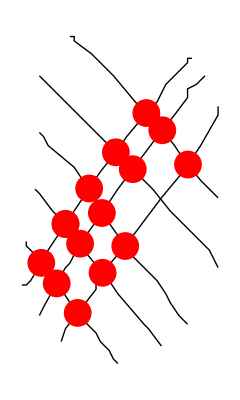

```mathematica
Graphics[{{Line[line1],Line[line2],Line[line3],Line[line4],Line[line5],Line[line6],Line[line7],Line[line8]},{Red,PointSize[0.05],Point/@ints1,Point/@ints2,Point/@ints3,Point/@ints4,Point/@ints5,Point/@ints6,Point/@ints7,Point/@ints8}}]
```

```mathematica
Length[line4]
```

16

```mathematica
Length[line8]
```

12

```mathematica
Take[line4,{10,11}]
```

{{320.,410.},{360.,360.}}

```mathematica
Take[line8,{6,7}]
```

{{250.,270.},{340.,390.}}

```mathematica
intersection[{{320.,410.},{360.,360.}},{{250.,270.},{340.,390.}}]
```

{338.065,387.419}

```mathematica
ints8
```

{{148.,126.},{205.,218.},{257.059,279.412},{400.909,466.364}}

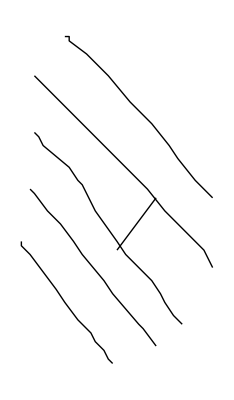

```mathematica
Graphics[{{Line[line1],Line[line2],Line[line3],Line[line4],Line[line5],Line[Take[line8,{6,7}]]}}]
```

## prob 2

```mathematica
Length[line2]
```

15

```mathematica
Length[line6]
```

18

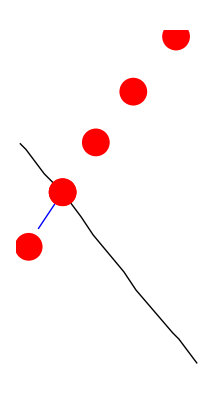

```mathematica
Graphics[{{Line[Take[line2,{1,15}]],Blue,Line[Take[line6,{5,6}]]},{Red,PointSize[0.05],Point/@ints6}}]
```

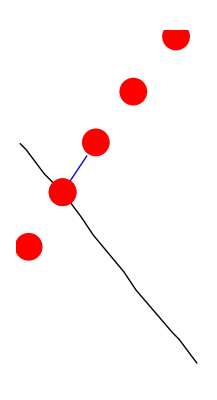

```mathematica
Graphics[{{Line[Take[line2,{1,15}]],Blue,Line[Take[line6,{6,7}]]},{Red,PointSize[0.05],Point/@ints6}}]
```

```mathematica
ints6
```

{{64.4444,240.741},{120.,330.},{120.,330.},{174.286,411.429},{235.556,494.444},{305.455,584.545}}

```mathematica
Take[line6,{5,6}]
```

{{80.,270.},{120.,330.}}